# Generic Natario warp drive

## The metric

```mathematica
ClearAll[v,xi];
xi={t,x,y,z};
v={vx[t,x,y,z],vy[t,x,y,z],vz[t,x,y,z]};

ClearAll[gUU,gLL];
gUU={
{-1,-v[[1]],-v[[2]],-v[[3]]},
{-v[[1]],1-v[[1]]v[[1]],-v[[1]]v[[2]],-v[[1]]v[[3]]},
{-v[[2]],-v[[2]]v[[1]],1-v[[2]]v[[2]],-v[[2]]v[[3]]},
{-v[[3]],-v[[3]]v[[1]],-v[[3]]v[[2]],1-v[[3]]v[[3]]}
};

gLL=FullSimplify[Inverse[gUU]];

ClearAll[Γ];
Γ=ParallelTable[
FullSimplify[1/2Sum[gUU[[i,m]](D[gLL[[m,k]],xi[[l]]]+D[gLL[[m,l]],xi[[k]]]-D[gLL[[k,l]],xi[[m]]]),{m,1,4}]],
{i,1,4},
{k,1,4},
{l,1,4}
];
```

## Particle Hamiltonian

```mathematica
ClearAll[p,q];
p={pt,px,py,pz};
q={t,x,y,z};

ClearAll[H];
H=FullSimplify[1/2Sum[gUU[[a,b]]p[[a]]p[[b]],{a,1,4},{b,1,4}]];

ClearAll[dHdp];
dHdp=FullSimplify[Table[D[H,p[[i]]],{i,1,4}]];

ClearAll[dHdq];
dHdq=FullSimplify[Table[D[H,q[[i]]],{i,1,4}]];

ClearAll[restoreLambda];
restoreLambda={pt->pt[λ],px->px[λ],py->py[λ],pz->pz[λ],t->t[λ],x->x[λ],y->y[λ],z->z[λ]};

ClearAll[state,lhs,rhs];
state={pt[λ],px[λ],py[λ],pz[λ],t[λ],x[λ],y[λ],z[λ]};
lhs=D[state,λ];
rhs=(Join[-dHdq,dHdp]/.restoreLambda);
```

## Bubble transition functions

### Sharp transition

```mathematica
(*https://www.j-raedler.de/2010/10/smooth-transition-between-functions-with-tanh*)
(*https://en.wikipedia.org/wiki/Non-analytic_smooth_function#Smooth_transition_functions*)
ClearAll[SNAf,SNAg,SNAh];
SNAf[x_]:=Piecewise[{{Exp[-1/x],x>0},{0,x≤0}}];
SNAg[x_]:=SNAf[x]/(SNAf[x]+SNAf[1-x]);
SNAh[xa_,xb_,x_]:=SNAg[(x-xa)/(xb-xa)];

ClearAll[T];
T[a_,xa_,b_,xb_,x_]:=b*SNAh[xa,xb,x]+(1-SNAh[xa,xb,x])a;

ClearAll[TopHat];
TopHat[σ_,R_,x_]:=T[0,-σ,1,-R,x]T[1,R,0,σ,x];
```

```mathematica
ClearAll[th];
th=FullSimplify[TopHat[σ,R,x],{σ∈Reals,R∈Reals,x∈Reals,σ>=0,R>=0,σ>R,x>=0}]
```

Piecewise[{{1/(1+ⅇ^(((R-σ) (R-2 x+σ))/((R-x) (x-σ)))), R<x&&x<σ}, {0, R<x}, {1, True}}]

```mathematica
ClearAll[dth];
dth=FullSimplify[Derivative[0,0,1][TopHat][σ,R,x],{σ∈Reals,R∈Reals,x∈Reals,σ>=0,R>=0,σ>R,x>=0}]
```

Piecewise[{{(ⅇ^(((R-σ) (R+σ))/((R-x) (x-σ))) (R-σ) (R^2-2 R x+2 x^2-2 x σ+σ^2))/((ⅇ^(R/(x-σ)+σ/(R-x))+ⅇ^(R/(R-x)+σ/(x-σ)))^2 (R-x)^2 (x-σ)^2), R<x&&x<σ}, {0, True}}]

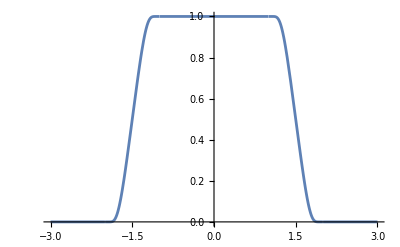

```mathematica
Plot[TopHat[2,1,x],{x,-3,3}]
```

## Eulerian observer

```mathematica
ClearAll[uL,uU];
uL={-1,0,0,0};
uU=Table[Sum[gUU[[a,b]]uL[[b]],{b,1,4}],{a,1,4}]
```

{1,vx[t,x,y,z],vy[t,x,y,z],vz[t,x,y,z]}

The Eulerian observer is a solution of the geodesic equation

```mathematica
FullSimplify[
Table[
Sum[uU[[b]](D[uL[[b]],xi[[1]]]-Sum[Γ[[i,b,a]]uL[[i]],{i,1,4}]),{a,1,4},{b,1,4}],{c,1,4}
]
]
```

{0,0,0,0}

## Alcubierre solution

### Constant of motion

```mathematica
ClearAll[vx,vy,vz];
vx[t_,x_,y_,z_]=V*f[r[t,x,y,z]];
vy[t_,x_,y_,z_]=0;
vz[t_,x_,y_,z_]=0;

ClearAll[dptdλ,dpxdλ,dpydλ,dpzdλ];
dptdλ=-D[H,t];
dpxdλ=-D[H,x];
dpydλ=-D[H,y];
dpzdλ=-D[H,z];


ClearAll[r];
r[t_,x_,y_,z_]=Sqrt[(x-V*t)^2+y^2+z^2];
FullSimplify[dptdλ+V*dpxdλ]
ClearAll[r];

ClearAll[dptdλ,dpxdλ,dpydλ,dpzdλ];
ClearAll[vx,vy,vz];
```

0

### Equations of motion

```mathematica
ClearAll[vx,vy,vz];
vx[t_,x_,y_,z_]=V*f[r[t,x,y,z]];
vy[t_,x_,y_,z_]=0;
vz[t_,x_,y_,z_]=0;

ClearAll[dptdλ,dpxdλ,dpydλ,dpzdλ];
dptdλ=FullSimplify[-D[H,t]];
dpxdλ=FullSimplify[-D[H,x]];
dpydλ=FullSimplify[-D[H,y]];
dpzdλ=FullSimplify[-D[H,z]];

ClearAll[dtdλ,dxdλ,dydλ,dzdλ];
dtdλ=FullSimplify[D[H,pt]];
dxdλ=FullSimplify[D[H,px]];
dydλ=FullSimplify[D[H,py]];
dzdλ=FullSimplify[D[H,pz]];

dptdλ//.{pt->-1,px->0}
dpxdλ//.{pt->-1}
dpydλ//.{pt->-1}

dtdλ

ClearAll[eqs];
ClearAll[dptdλ,dpxdλ,dpydλ,dpzdλ];
ClearAll[dtdλ,dxdλ,dydλ,dzdλ];
ClearAll[vx,vy,vz];
```

0

px V (-1+px V f[r[t,x,y,z]]) f'[r[t,x,y,z]] r^(0,1,0,0)[t,x,y,z]

px V (-1+px V f[r[t,x,y,z]]) f'[r[t,x,y,z]] r^(0,0,1,0)[t,x,y,z]

-pt-px V f[r[t,x,y,z]]

## Rust code strings

```mathematica
Unprotect[Power];
Format[Power[E,a_],CForm]:=exp[a];
Format[Power[a_,1/2],CForm]:=sqrt[a];
Format[Power[a_,b_],CForm]:=pow[a,b];
Format[Power[a_,2],CForm]:=(HoldForm[a*a]);
Format[Power[a_,-1],CForm]:=HoldForm[1/(a)];
Protect[Power];
```

```mathematica
ClearAll[rules];
rules={
D[vx[t,x,y,z],t]->dvxdt,
D[vx[t,x,y,z],x]->dvxdx,
D[vx[t,x,y,z],y]->dvxdy,
D[vx[t,x,y,z],z]->dvxdz,

D[vy[t,x,y,z],t]->dvydt,
D[vy[t,x,y,z],x]->dvydx,
D[vy[t,x,y,z],y]->dvydy,
D[vy[t,x,y,z],z]->dvydz,

D[vz[t,x,y,z],t]->dvzdt,
D[vz[t,x,y,z],x]->dvzdx,
D[vz[t,x,y,z],y]->dvzdy,
D[vz[t,x,y,z],z]->dvzdz,

vx[t,x,y,z]->lvx,
vy[t,x,y,z]->lvy,
vz[t,x,y,z]->lvz

};

Print["dHdpt = ",ToString[dHdp[[1]]//.rules,CForm]]
Print["dHdpx = ",ToString[dHdp[[2]]//.rules,CForm]]
Print["dHdpy = ",ToString[dHdp[[3]]//.rules,CForm]]
Print["dHdpz = ",ToString[dHdp[[4]]//.rules,CForm]]

Print["dHdqt = ",ToString[FullSimplify[dHdq[[1]]//.rules],CForm]]
Print["dHdqx = ",ToString[FullSimplify[dHdq[[2]]//.rules],CForm]]
Print["dHdqy = ",ToString[FullSimplify[dHdq[[3]]//.rules],CForm]]
Print["dHdqz = ",ToString[FullSimplify[dHdq[[4]]//.rules],CForm]]

ClearAll[HamCond];
HamCond=Collect[(H-δ/2)//.rules,pt,FullSimplify];

Print["a = ",ToString[Coefficient[HamCond,pt^2],CForm]]
Print["b = ",ToString[Coefficient[HamCond,pt],CForm]]
Print["c = ",ToString[HamCond//.pt->0,CForm]]

Print["Transition = ",
StringReplace[
ToString[FullSimplify[th,{R<x<σ}],CForm],
{
"1"->"1.0",
"2"->"2.0",
"x"->"rr",
"σ"->"radii.sigma",
"R"->"radii.radius",
"exp"->"f64::exp"
}
]
]

Print["Transition derivative = ",
StringReplace[
ToString[FullSimplify[dth,{R<x<σ}],CForm],
{
"2"->"2.0",
"x"->"rr",
"σ"->"radii.sigma",
"R"->"radii.radius",
"exp"->"f64::exp"
}
]
]

ClearAll[HamCond];
ClearAll[rules];
```

dHdpt = -pt - lvx*px - lvy*py - lvz*pz

dHdpx = px - lvx*(pt + lvx*px + lvy*py + lvz*pz)

dHdpy = py - lvy*(pt + lvx*px + lvy*py + lvz*pz)

dHdpz = pz - lvz*(pt + lvx*px + lvy*py + lvz*pz)

dHdqt = -((dvxdt*px + dvydt*py + dvzdt*pz)*(pt + lvx*px + lvy*py + lvz*pz))

dHdqx = -((dvxdx*px + dvydx*py + dvzdx*pz)*(pt + lvx*px + lvy*py + lvz*pz))

dHdqy = -((dvxdy*px + dvydy*py + dvzdy*pz)*(pt + lvx*px + lvy*py + lvz*pz))

dHdqz = -((dvxdz*px + dvydz*py + dvzdz*pz)*(pt + lvx*px + lvy*py + lvz*pz))

a = -0.5

b = -(lvx*px) - lvy*py - lvz*pz

c = (-((-1 + lvx*lvx)*(px*px)) - (-1 + lvy*lvy)*(py*py) - 2*lvy*lvz*py*pz + pz*pz - lvz*lvz*(pz*pz) - 2*lvx*px*(lvy*py + lvz*pz) - δ)/2.

Transition = 1.0/(1.0 + f64::exp(((radii.radius - radii.sigma)*(radii.radius - 2.0*rr + radii.sigma))/((radii.radius - rr)*(rr - radii.sigma))))

Transition derivative = (f64::exp(((radii.radius - radii.sigma)*(radii.radius + radii.sigma))/((radii.radius - rr)*(rr - radii.sigma)))*(radii.radius - radii.sigma)*(radii.radius*radii.radius - 2.0*radii.radius*rr + 2.0*(rr*rr) - 2.0*rr*radii.sigma + radii.sigma*radii.sigma))/((f64::exp(radii.radius/(rr - radii.sigma) + radii.sigma/(radii.radius - rr)) + f64::exp(radii.radius/(radii.radius - rr) + radii.sigma/(rr - radii.sigma)))*(f64::exp(radii.radius/(rr - radii.sigma) + radii.sigma/(radii.radius - rr)) + f64::exp(radii.radius/(radii.radius - rr) + radii.sigma/(rr - radii.sigma)))*((radii.radius - rr)*(radii.radius - rr))*((rr - radii.sigma)*(rr - radii.sigma)))